```mathematica
HRT PROBLEM
```

RANDOM DATA GENERATION

```mathematica
(*Input of hospitals and residents quantities*)
R=50;
H=10;

(*Initialisation of preferenses with epmty list for each hospital/resident*)
GeneratedRprefs = Table[List[],{i,R}];
GeneratedHprefs=Table[List[],{i,H}];

(*Initialisation of quotas for each hospital*)
GeneratedQuotas=Table[1,{i,H}];

(*Manually set distribution parameters for dataset*)
QuotaLimit = 7;
RTDP= 20; (*ResidentsTiesDistributionParameter *)
HTDP= 50; (*HospitalsTiesDistributionParameter *)


(*Table of applications to hospitals by residents, required for generation a consistent dataset*)
AppliedResidentsTable = Table[List[],{i,H}];

(*RESIDENTS PREFERENCES GENERATION LOOP*)
For[thisResident=1, thisResident ≤R,thisResident ++,

	thisResidentPrefLength = RandomInteger[{1,H}];
	k = RandomSample[Range[H],thisResidentPrefLength]; (*Random sample without ties*)
	GeneratedRprefs[[thisResident]] = k;

	AppliedResidentsTable[[k]] = Map[Append[#,thisResident]&,AppliedResidentsTable[[k]] ];
	GeneratedRprefs[[thisResident]] =  GatherBy[GeneratedRprefs[[thisResident]],RandomInteger[RTDP]&];  (*Sample gathered in ties randomly*)
]

(*HOSPITALS PREFERENCES AND QUOTAS GENERATION LOOP*)
For[thisHospital=1, thisHospital ≤H,thisHospital++,
		
		GeneratedQuotas[[thisHospital]] =  RandomInteger[{1,QuotaLimit}]; (*Random quota value*)
		
		(*Random sample without ties from applicants to this Hospital. Thus we garantee preference list are consistent*)
		GeneratedHprefs[[thisHospital]] =RandomSample[AppliedResidentsTable[[thisHospital]] ] ;

		GeneratedHprefs[[thisHospital]] =  GatherBy[GeneratedHprefs[[thisHospital]],RandomInteger[HTDP]&];   (*Sample gathered in ties randomly*)
]
```

GENERATED DATA

```mathematica
(*remove semicolon to observe*)
MatrixForm[GeneratedRprefs]
MatrixForm[GeneratedHprefs]
MatrixForm[GeneratedQuotas]
```

({{9},{8},{10},{1},{2},{6},{7},{4},{3},{5}}
{{4},{9},{7}}
{{3}}
{{3},{10,8},{7},{2},{5},{4},{6,9}}
{{3},{4},{10},{2,9},{1},{7}}
{{6,2},{4,3},{5},{8,10},{9},{7,1}}
{{4,3},{5},{1}}
{{10},{3},{9},{2},{4}}
{{2},{6},{8},{10}}
{{3}}
{{7}}
{{5},{3},{1}}
{{4},{9},{10},{3,1},{2},{6},{5},{8},{7}}
{{8},{10},{3}}
{{9},{8}}
{{5},{3},{9}}
{{1},{3},{9}}
{{10},{8},{7},{6},{4}}
{{4,5},{3},{10},{2},{1},{9},{7},{8}}
{{5},{8},{10},{9}}
{{8},{1},{4},{5},{10},{6},{7}}
{{4},{9}}
{{4}}
{{5},{6},{1},{4},{10},{8},{2}}
{{4,8},{1},{9},{6},{10},{3}}
{{1,3},{10},{5},{9},{4},{2}}
{{3,2},{9},{1},{4},{5},{7}}
{{4},{9,1},{3},{5},{8},{7},{6},{10}}
{{8},{4},{1},{6,9},{2},{3}}
{{10},{2},{9},{3},{7},{4}}
{{3},{7,6},{10},{2},{9},{5},{8},{1},{4}}
{{4},{10},{7},{8},{1},{6},{9},{5}}
{{1},{3,4},{10},{5,7},{9},{6},{2}}
{{4}}
{{1,4,9},{2},{5},{3},{7},{6},{10}}
{{2}}
{{6},{4},{8},{7},{3}}
{{6,7},{4},{1},{8},{9},{5},{10,3},{2}}
{{7}}
{{6},{7},{4},{3,5},{8},{2},{10}}
{{1},{8,2},{10,4},{6},{9},{3},{7},{5}}
{{2}}
{{4,1},{10},{9},{2},{8}}
{{4,1},{7},{8},{3},{2},{9,6,10},{5}}
{{9},{7}}
{{9}}
{{2},{3},{5},{6,9},{7},{4},{1},{10},{8}}
{{8}}
{{6,1},{9},{4,10},{2},{5},{3}}
{{10},{9},{1}})

({{19,29},{13},{7},{33},{38},{5},{28,25},{41,44},{24},{43,21,35},{32},{31},{50},{27},{26},{1,49},{47},{17},{12},{6}}
{{19},{29,5},{40},{13},{35,30},{31,9},{38,8},{1},{44},{49},{41},{4},{24},{47},{26},{33},{27},{42},{43,36},{6}}
{{26,49},{17},{5},{4,41},{33},{31,40},{44},{35},{12},{19},{16,38},{29},{28},{6},{13},{14},{8},{37,25},{47},{1},{10,30},{27},{7},{3}}
{{47,23},{2},{22},{35},{40},{44},{41},{5,8},{43},{19,28},{34,32},{37},{18},{27,7},{4,13},{30,38},{6,25},{49},{21},{29},{31,1},{33,24},{26}}
{{38,47},{41,49},{32},{24},{4,26},{16,28},{31},{6,20},{44,1},{12,7},{13},{27,40},{19},{35},{33},{21}}
{{32,33},{44,35},{37},{6},{4},{18},{21,31},{49,1},{29},{38,41},{28,47},{40},{24},{13},{25},{9}}
{{2,35},{30},{28,13},{11},{39},{4,37,6},{18,41},{47},{32},{45,40,19},{31},{38},{44,1,5},{33},{21},{27}}
{{18},{47},{44},{48,41},{24},{9,25},{28},{14},{29},{37,1},{31},{20,6,43,32},{15},{19},{40},{38},{4},{21},{13}}
{{6},{49,19},{41},{32},{50},{47,13},{27,1},{38,5,4},{26},{29,43},{2},{16,33},{44},{25},{46},{8},{20},{35},{31},{15},{28},{17},{30},{22},{45}}
{{35,14},{43},{28},{32,49},{30},{50},{21},{9},{31},{41,24},{4},{20},{6},{33},{38},{47},{44},{40},{19,13},{5},{8},{25},{1},{26},{18}})

(6
1
2
3
2
4
3
7
2
7)

```mathematica
FUNCTIONS
```

```mathematica
(*Find an alternating path with respect to Matching from resident rN to hospital hN
Returns the first found alternating pathas a list of edges
 OR empty list {} if nothing found *)

FindAlternatingPath[GRAPH_, startVertice_,finalVertice_, Matching_]:=
Module[
{G=GRAPH,s= startVertice,f= finalVertice},

(*find all paths and represent it as a list of edges*)
paths=FindPath[G, s, f,2*H,All];
pathsAsEdgeLists = EdgeList/@(PathGraph/@paths);

path ={};

(*Loop over all found paths*)
For[k=1, k<=Length[paths],k++,

path =pathsAsEdgeLists[[k]];

OddEdgesInPath = path [[1;;;;2]]; (* 1st, 3rd, 5th ... edges*)
EvenEdgesInPath = path [[2;;;;2]];(* 2nd, 4th, 6th ... edges*)

EvenEdgesInPath =EdgeList[PathGraph[Reverse[VertexList[EvenEdgesInPath]]]] ;
path [[2;;;;2]]= EvenEdgesInPath;
(*a crutch that is necessary so that there is always a resident at the beginning of the edge and checking the set of edges for the fact that this is a matching subset was correct*)

(*Check if the path is alternating*)
If [SubsetQ[Matching, EvenEdgesInPath]&&Intersection[OddEdgesInPath ,Matching]=={},
(*Yes.  break cycle and return this path*)
Break[];
,
(*No. Discard the path*)
path ={};
];
];
Return[path,Module]
];
```

```mathematica
FindMaximumMatching[listG_,GRAPH_,RevisedQuotas_]:=
Module[
{lG = listG,G=GRAPH,RQ =RevisedQuotas},
M ={};
U = {}; (*Unassigned*)
Uprime={};(*U' - reachable from this unassigned residents via alternating paths*)


GRResidents =DeleteDuplicates[Flatten[lG]];
GRHospitals = Select[Range[H],(lG[[#]]!={})&];

For[i=1,i≤Length[GRResidents],i++,
r=GRResidents[[i]];
p = {};

For[j=1,j≤Length[GRHospitals],j++,
h =GRHospitals[[j]];

residentVertice = "r"<>ToString[r];
hospitalVertice = "h"<>ToString[h];

If[RQ[[h]]≥1,

p = FindAlternatingPath[G, residentVertice,hospitalVertice, M];

If[p≠{},
(*resident r has  alternating path to free hospital *)
M = Complement[Union[M,p],Intersection[M,p]]; (*XOR of matching M and path p*)
RQ[[h]] -=1;
Break[]
];
];

If[j==Length[GRHospitals]&&p == {},
(*resident r has no alternating paths to free hospitals *)
AppendTo[U,r];

(*Find U'  - reachable from this unassigned resident via alternating path*)
For[l=1,l≤Length[GRResidents ],l++,
rZcandidate=GRResidents [[l]];
rZcandidateVertice = "r"<>ToString[rZcandidate];

If[FindAlternatingPath[G, residentVertice,rZcandidateVertice, M]≠{},
AppendTo[Uprime,rZcandidate];
];
];
];
];
];

Z = Union[U,Uprime];

Print["Critical set Z =", Z];
Return[M,Module]
]
```

ALGORITHM

-------------------------------------------

ITERATION 1

Provisional assignment graph  G= {{33,41,44,7,28,38,5},{19},{26,17},{2,22,23},{24,47},{6,37,49,31},{11,39,35},{14,25,29,48,20,18,9},{1,13,27},{30,50,4,32,21,43,40}}

Reduced Graph  GR= {{41,44},{},{},{},{},{},{},{},{1,27},{}}

Critical set Z ={1,27,41,44}

Matching in GR

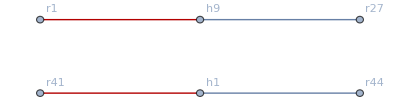

-------------------------------------------

ITERATION 2

Provisional assignment graph  G= {{33,7,28,38,5,29},{19},{26,17},{2,22,23},{24,47},{6,37,49,31,1},{11,39,35},{14,25,48,18,9,41,44},{13},{30,50,4,32,21,43,20}}

Reduced Graph  GR= {{},{},{},{},{},{49,1},{},{},{},{}}

Critical set Z ={1,49}

Matching in GR

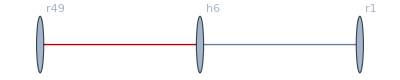

-------------------------------------------

ITERATION 3

Provisional assignment graph  G= {{33,7,28,38,5,29},{19},{26,17},{2,22,23},{24,47},{6,37,31},{11,39,35},{14,25,48,18,9,41,44},{13,49},{30,50,4,32,21,43,20}}

Reduced Graph  GR= {{},{},{},{},{},{},{},{},{},{}}

Critical set Z ={}

Matching in GR

-Graphics-

```mathematica
Rprefs= GeneratedRprefs;
Hprefs = GeneratedHprefs;
Quotas = GeneratedQuotas;


Z = Range[R];
G=  Table[List[],{i,H}]; (*Provisional assignment graph *)
GR= G;
z =1;

While[Z != {},
Print ["-------------------------------------------"];
Print ["ITERATION ", z];
(* G=  Table[List[],{i,H}]; Provisional assignment graph *)

 	For[j=1,j<20,j++,
		(* Provisional assignment iterantion j .Build provisional assignment graph *)
		For[r=1,r≤R,r++,
			If [Position[G,r]=={} && Rprefs[[r]]≠{},
				rh = Rprefs[[r]][[1]];

				G[[rh]] = Map[Append[#,r]&,G[[rh]] ];
			];
		];
		(*Print["G = ", G];*)

		(*Loop over hospitals to find replete ones *)
		For[h=1,h<=H,h++,
			If[Length[G[[h]]]≥Quotas[[h]], (* Hospital  h is replete*)

				(*Loop over residents from Hprefs to find dominated ones in current replete hospital h*)
				HprefsFlattened = Flatten[Hprefs[[h]]];
				
				For[i=1,i<=Length[HprefsFlattened],i++,
						r = HprefsFlattened[[i]];
						pos= Position[Hprefs[[h]],r];
						p = pos[[1]][[1]];
					
						ResidentsBetter =Flatten[Hprefs[[h]][[Range[p-1] ]] ]; (*all resident better*)
						ProvisionallyAssignedResidentsBetter = Intersection[ResidentsBetter, G[[h]] ] ;(*intersection with provisionally assigned*)
						l =Length[ ProvisionallyAssignedResidentsBetter];
						
						If[l≥Quotas[[h]],
							(*Print["resident №", r, " is dominated in hospital  №", h, ". Deletion..."];*)
							
							(*Delete them from one another's preference lists*)
							Hprefs[[h]] =Replace[ Delete[ Hprefs[[h]],pos], {}->Nothing,{1,2}]; (*replace with levelspec = {1,2} deletes empty ties*)
							
							
							Rprefs[[r]] = Replace[Delete[ Rprefs[[r]],Position[Rprefs[[r]],h]], {}->Nothing,{1,2}]; (*replace with levelspec = {1,2} deletes empty ties*)
							
							(*If r is provisionally assigned to h,the breaking of this provisional assignment *)
							If [Position[G[[h]],r]≠{},
								G[[h]] = Delete[G[[h]], Position[G[[h]],r] ];
							];
						];
					];
				];
			];
		];

		(*Build REDUCED provisional assignment graph *)
				GR = G;
				
				RevisedQuotas = Quotas;
				For[h=1,h<=H,h++,
					If[GR[[h]]≠{},
						ProvisionallyAssignedResidents = GR[[h]];
						For[k=1,k<=Length[ ProvisionallyAssignedResidents],k++,
							
							r = ProvisionallyAssignedResidents[[k]];

							pos= Position[Hprefs[[h]],r];
							p = pos[[1]][[1]];
						
							If[(Length[GR[[h]]]<=RevisedQuotas[[h]]) ||(p<Length[Hprefs[[h]]]),
								(*Removing *)
								GR = Delete[GR, Position[GR,r] ];
								RevisedQuotas[[h]] -= 1;
							];
							
							If[RevisedQuotas[[h]] == 0,
								GR[[h]]={};
								Break[];
							];
						];
					];
				];
			Print["Provisional assignment graph  G= ",G];
			Print["Reduced Graph  GR= ",GR];
		GREdges = Flatten[Table[Table[("r"<>ToString[ GR[[i]][[j]] ])<->("h"<>ToString[i]),{j,Length[GR[[i]]] } ],{i,Length[GR]}],2];
		GRgraph=Graph[GREdges, VertexLabels->"Name"];

		(*Find matching and critical set Z*)
		M =FindMaximumMatching[GR,GRgraph,RevisedQuotas];

		Print["Matching in GR"];
		Print[HighlightGraph[GRgraph,M]];
  		ZVertex = Table["r"<>ToString[ Z[[i]] ],{i,Length[Z]}];

		(*Find N(Z) *)
		NG =NeighborhoodGraph[GRgraph,ZVertex ];
		NofZ =Select[VertexList[NG ],StringTake[#,1]=="h"&];

		(*Find N(Z) as a number list, not {"h22", "h145"} form *)
		NZlist =ToExpression[StringDrop[NofZ,1] ];

		(*DELETE TAILS *)

		For[hv=1,hv≤Length[NZlist],hv++,

			h =NZlist[[hv]];
			rdeletionlist = DeleteDuplicates[Flatten[Hprefs[[h,-1]] ,3]];

			(*If r is provisionally assigned to h,the breaking of this provisional assignment *)
			For[dr = 1, dr ≤Length[rdeletionlist], dr++,
				delr =rdeletionlist[[dr]];
				
				If [Position[G[[h]],delr ]≠{},
				G[[h]] = Delete[G[[h]], Position[G[[h]],delr] ];
					];
			];

		(*Delete them from one another's preference lists*)
		pos=Position[Rprefs[[  Hprefs[[h,-1]]  ]],h];
		Rprefs[[  Hprefs[[h,-1]] ]] =Replace[Delete[ Rprefs[[  Hprefs[[h,-1]] ]],pos],{}->Nothing, {2,3}]; (*replace with levelspec = {2,3} deletes empty ties*)  

		Hprefs[[h]] =Replace[ Delete[ Hprefs[[h]],-1], {}->Nothing,{2,3}]; (*replace with levelspec = {1,2} deletes empty ties*) 
			];щ
	z++;
];
```

Critical set Z ={}

Strong stable matching:

(r11<->h7
r13<->h9
r14<->h8
r17<->h3
r18<->h8
r19<->h2
r2<->h4
r20<->h10
r21<->h10
r22<->h4
r23<->h4
r24<->h5
r25<->h8
r26<->h3
r28<->h1
r29<->h1
r30<->h10
r31<->h6
r32<->h10
r33<->h1
r35<->h7
r37<->h6
r38<->h1
r39<->h7
r4<->h10
r41<->h8
r43<->h10
r44<->h8
r47<->h5
r48<->h8
r49<->h9
r5<->h1
r50<->h10
r6<->h6
r7<->h1
r9<->h8)

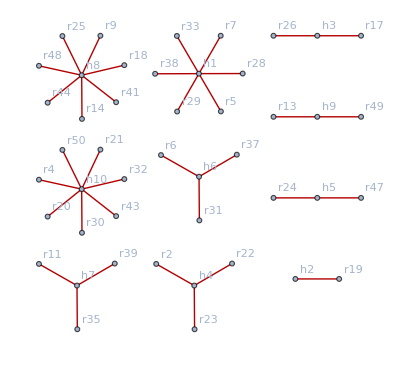

```mathematica
(*Feasible matching in provisional assignment graph*)
GEdges = Flatten[Table[Table[("r"<>ToString[ G[[i]][[j]] ])<->("h"<>ToString[i]),{j,Length[G[[i]]] } ],{i,Length[G]}],2];
Ggraph=Graph[GEdges, VertexLabels->"Name"];
Matching =FindMaximumMatching[G,Ggraph,Quotas];

(*Calculating Req - required number of residents in matching for hospitals - the vertex degree in G or its quota for each particular h *)
HospitalVertices= Select[VertexList[Ggraph],StringTake[#,1]=="h"&];
HospitalDegrees = Table[VertexDegree[Ggraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];
MatchingGraph = Graph[Matching , VertexLabels->"Name"];
MatchingHospitalDegrees = Table[VertexDegree[MatchingGraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];

QuotasForGraphHospitals = Quotas[[ToExpression[StringDrop[HospitalVertices,1] ]]];
Req = MapThread[Min,{HospitalDegrees,QuotasForGraphHospitals}] ; 


(*ANSWER*)
If [Max[Req - MatchingHospitalDegrees]>0,
Print["No strongly stable matching exists"];
Print[Ggraph];
,
Print["Strong stable matching:"];
Print[MatrixForm[Matching]];

Mgraph = HighlightGraph[Ggraph,Matching ];

Print[Mgraph];

];
```